## For "Pound-Drever-Hall" (Problem 11.20)

```mathematica
Clear["Global`*"];
f=1/((1-ω^2)^2+4 ζ^2 ω^2);f1=D[f, ω]//Simplify;f2=D[f, ω,ω]//Simplify;
{f1,f2}
```

{-(4 ω (-1+2 ζ^2+ω^2))/((1+(-2+4 ζ^2) ω^2+ω^4)^2),(96 ζ^4 ω^2+4 (-1+ω^2)^2 (1+5 ω^2)+8 ζ^2 (-1-12 ω^2+9 ω^4))/((1+(-2+4 ζ^2) ω^2+ω^4)^3)}

```mathematica
f2res=f2/.ω->√(1-2 ζ^2)//Simplify
```

(-1+2 ζ^2)/(2 ζ^4 (-1+ζ^2)^2)

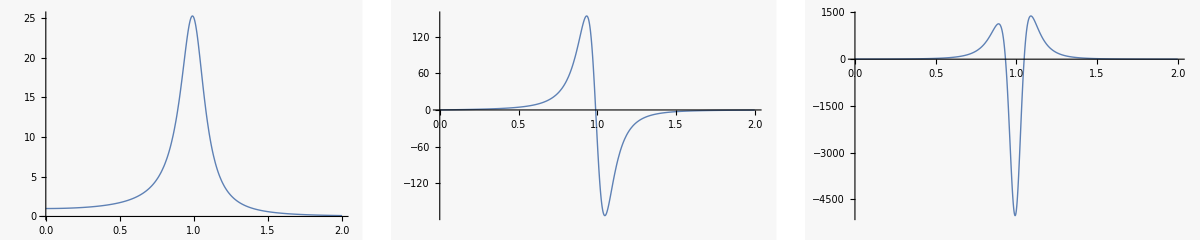

```mathematica
p1=Plot[f/.ζ->0.1,{ω,0,2},PlotRange->All];
p2=Plot[f1 /. ζ -> 0.1, {ω, 0, 2}, PlotRange->All];
p3=Plot[f2/.ζ->0.1,{ω,0,2},PlotRange->All];
GraphicsRow[{p1,p2,p3}]
```

```mathematica
den=Series[((1-ω^2)^2+4 ζ^2 ω^2)^2/.ω->1+ζ/(√3)//Simplify,{ζ,0,5}]
```

(256 ζ^4)/9+(896 ζ^5)/(9 √3)+O[ζ]^6

```mathematica
num=Series[4 ω (-1+2 ζ^2+ω^2)/.ω->1+ζ/(√3),{ζ,0,5}]
```

(8 ζ)/(√3)+12 ζ^2+(28 ζ^3)/(3 √3)+O[ζ]^6

```mathematica
N[9/(32 √3)1000]
```

162.38

error signal (compare Taylor expansion to no expansion and to 2nd derivative linearization)

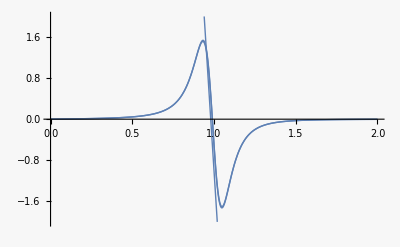

```mathematica
ff[ω_]=1/((1-ω^2)+2ⅈ ζ ω);
Plot[{Re[ff[ω] ff[ω+Ω]*-ff[ω]* ff[ω-Ω]],Ω f1,Ω f2res(ω-1+2 ζ^2)}/.{ζ->0.1,Ω->0.01},{ω,0,2},PlotRange->{-2,2}]
```